```mathematica
σ=π/4;(*initial wobble angle*)
ω0=200;(*initial angular velocity in body frame*)
I0=10^45;
I1=I0*(1-10^-6);
I2=1*I0;
I3=I0*(1+2*10^-6);
a=ω0*Sin[σ];
w20=0;
b=ω0*Cos[σ];
J= (I1^2*a^2+I2^2*w20^2+I3^2*b^2)^0.5;
E0=1/2 I1*a^2+1/2 I2*w20^2+1/2 I3*b^2;
k2=((I2-I1)(2E0*I3-J^2))/((I3-I2)(J^2-2E0*I1));
taut=√(((I3-I2)(J^2-2E0*I1))/(I1*I2*I3));
K=EllipticK[k2];
T=4*K*((I1*I2*I3)/((I3-I2)*(J^2-2*E0*I1)))^0.5;
x1=I* (I3*b)/(I1*a);
α= Re[InverseJacobiSN[x1,k2]/I/K/2];
q= Exp[-π* EllipticK[1-k2]/EllipticK[k2]];
T1=2π/Re[(J/I1-2*I/T*EllipticThetaPrime[4,π*α*I,q]/EllipticTheta[4,π*α*I,q])];
dt=T/10000;
n=1;(*number of free precession period *)
w1=Table[a*JacobiCN[t*taut,k2],{t,0,n*T,dt}];
w2=Table[a*√((I1(I3-I1))/(I2(I3-I2)))*JacobiSN[t*taut,k2],{t,0,n*T,dt}];
w3=Table[b*JacobiDN[t*taut,k2],{t,0,n*T,dt}];
time=Table[t,{t,0,n*T,dt}];
cosθ=Table[I3*b/J*JacobiDN[t*taut,k2],{t,0,n*T,dt}];
sinθ=Sin[ArcCos[Table[I3*b/J*JacobiDN[t*taut,k2],{t,0,n*T,dt}]]];
cosψ=Cos[ArcTan[Table[√((I1(I3-I2))/(I2(I3-I1)))JacobiCN[t*taut,k2]/JacobiSN[t*taut,k2],{t,0,n*T,dt}]]]*Sign[Floor[time/T]*T+T/2-time];
sinψ=Sin[ArcTan[Table[√((I1(I3-I2))/(I2(I3-I1)))JacobiCN[t*taut,k2]/JacobiSN[t*taut,k2],{t,0,n*T,dt}]]]*Sign[Floor[time/T]*T+T/2-time];
cosϕ1=Cos[ArcCos[Table[Re[EllipticTheta[4,2*π/T*t-π*α*I,q]/EllipticTheta[4,2*π/T*t+π*α*I,q]],{t,0,n*T,dt}]]/2];
sinϕ1=Sin[ArcSin[Table[Im[EllipticTheta[4,2*π/T*t-π*α*I,q]/EllipticTheta[4,2*π/T*t+π*α*I,q]],{t,0,n*T,dt}]]/2];
sinϕ2=Sin[Re[Table[(J/I1-2*I/T*EllipticThetaPrime[4,π*α*I,q]/EllipticTheta[4,π*α*I,q])*t,{t,0,n*T,dt}]]];
cosϕ2=Cos[Re[Table[(J/I1-2*I/T*EllipticThetaPrime[4,π*α*I,q]/EllipticTheta[4,π*α*I,q])*t,{t,0,n*T,dt}]]];
cosϕ=cosϕ1*cosϕ2-sinϕ1*sinϕ2;
sinϕ=sinϕ1*cosϕ2+cosϕ1*sinϕ2;
R11=cosψ*cosϕ-cosθ*sinψ*sinϕ;
R12=-sinψ*cosϕ-cosθ*cosψ*sinϕ;
R13=sinθ*sinϕ;
R21=cosψ*sinϕ+cosθ*sinψ*cosϕ;
R22=-sinψ*sinϕ+cosθ*cosψ*cosϕ;
R23=-sinθ*cosϕ;
R31=sinθ*sinψ;
R32=sinθ*cosψ;
R33=cosθ;
```

Power::infy: 碰到无穷表达式 1/0..

T is the free precession period. T1 is the rotational period.

```mathematica
T
T1
```

21409.

0.0314159

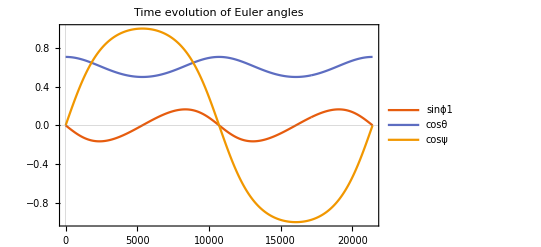

```mathematica
first1=Transpose@{time,sinϕ1};
first2=Transpose@{time,cosϕ2};
second=Transpose@{time,cosθ};
third=Transpose@{time,cosψ};
ListPlot[{first1,second,third},Joined->True, PlotLegends->{"sinϕ1","cosθ","cosψ"},PlotLabel->"Time evolution of Euler angles",PlotTheme->"Scientific",Axes->{True,False}]
```

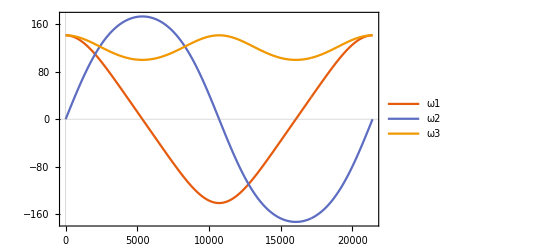

```mathematica
ω1=Transpose@{time,w1};
ω2=Transpose@{time,w2};
ω3=Transpose@{time,w3};
ListPlot[{ω1,ω2,ω3},Joined->True,PlotLegends->{"ω1","ω2","ω3"},PlotTheme->"Scientific"]
```

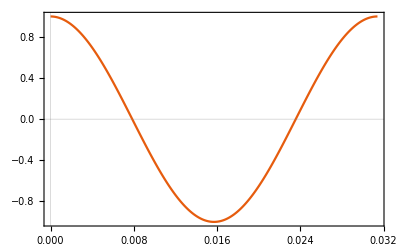

```mathematica
dt=T1/1000;
n=T1/T;(*number of free precession period *)
time=Table[t,{t,0,T1,dt}];
sinϕ2=Sin[Re[Table[(J/I1-2*I/T*EllipticThetaPrime[4,π*α*I,q]/EllipticTheta[4,π*α*I,q])*t,{t,0,n*T,dt}]]];
cosϕ2=Cos[Re[Table[(J/I1-2*I/T*EllipticThetaPrime[4,π*α*I,q]/EllipticTheta[4,π*α*I,q])*t,{t,0,n*T,dt}]]];
fourth=Transpose@{time,cosϕ2};
ListPlot[fourth,Joined->True,PlotTheme->"Scientific",PlotLegends->"cosϕ2"]
```